-Graphics3D-

-Graphics3D-

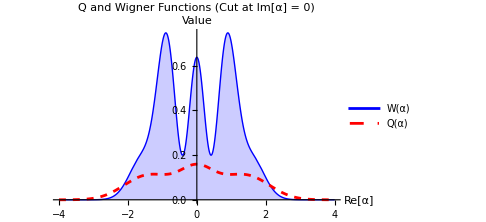

```mathematica
(*Definition of phase space coordinates*)x[a_,b_]:=a
y[a_,b_]:=b
r2[a_,b_]:=a^2+b^2

(*--------------------------------------------------------*)
(*1. Q function (Husimi) for superposition state (|0⟩+ |4⟩)/√2*)
(*Q(α)=1/(2π)*Exp[-|α|^2]*[1+ |α|^8/24+(2 Re[α^4])/√24]*)

QFunction0Plus4[a_,b_]:=(1/(2*Pi))*Exp[-r2[a,b]]*(1+(r2[a,b]^4)/24+(2/Sqrt[5])*Re[(a+I*b)^4])

(*--------------------------------------------------------*)
(*2. Wigner function for superposition state (|0⟩+ |4⟩)/√2*)
(*W(α)=1/π*Exp[-2|α|^2]*[1+L_4(4|α|^2)+(32 Re[α^4])/√24]*)

WignerFunction0Plus4[a_,b_]:=(1/Pi)*Exp[-2*r2[a,b]]*(1+LaguerreL[4,4*r2[a,b]]+(32/Sqrt[5])*Re[(a+I*b)^4])

(*--------------------------------------------------------*)
(*a) Plot Q function*)

Plot3D[QFunction0Plus4[a,b],{a,-4,4},{b,-4,4},PlotRange->All,ColorFunction->"BlueGreenYellow",Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","Q(α)"},PlotLabel->Style["Q Function for State (|0⟩ + |4⟩)/√2",Bold,14],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*b) Plot Wigner function*)

Plot3D[WignerFunction0Plus4[a,b],{a,-4,4},{b,-4,4},PlotRange->All,ColorFunction->"TemperatureMap",(*To emphasize negative regions*)Mesh->None,AxesLabel->{"Re[α] (X1)","Im[α] (X2)","W(α)"},PlotLabel->Style["Wigner Function for State (|0⟩ + |4⟩)/√2 (Strong Nonclassical Interference)",Bold,14,Red],BoxRatios->{1,1,0.5},ImageSize->Large]

(*--------------------------------------------------------*)
(*c) 2D slice to display negative values and symmetry (along Re[α] axis)*)

Plot[{WignerFunction0Plus4[x,0],QFunction0Plus4[x,0]},{x,-4,4},PlotLabel->Style["Q and Wigner Functions (Cut at Im[α] = 0)",Bold,14],PlotLegends->{"W(α)","Q(α)"},AxesLabel->{"Re[α]","Value"},GridLines->{None,{0}},PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red]},Filling->{1->Axis},ImageSize->Medium]
```